```mathematica
Table[With[{f=First[FindFullFormula4[MinimalGraph[k]]]},
Framed[f->Column[Sort[FinerSymbols[f]]]]
],{k,4,10}]//TableForm
```

v1x2x35x4→v1x2x3x4x5
v1x2x35x46→v1x2x35x4x6
v1x2x3x46x5
v1x2x357x46→v1x2x357x4x6
v1x2x35x46x7
v1x2x37x46x5
v1x2x3x46x57
v1x2x357x468→v1x2x357x46x8
v1x2x357x48x6
v1x2x357x4x68
v1x2x35x468x7
v1x2x37x468x5
v1x2x3x468x57
v1x2x3579x468→v1x2x3579x46x8
v1x2x3579x48x6
v1x2x3579x4x68
v1x2x357x468x9
v1x2x359x468x7
v1x2x35x468x79
v1x2x379x468x5
v1x2x37x468x59
v1x2x39x468x57
v1x2x3x468x579
v1x2x3579x468a→v1x2x3579x468xa
v1x2x3579x46ax8
v1x2x3579x46x8a
v1x2x3579x48ax6
v1x2x3579x48x6a
v1x2x3579x4ax68
v1x2x3579x4x68a
v1x2x357x468ax9
v1x2x359x468ax7
v1x2x35x468ax79
v1x2x379x468ax5
v1x2x37x468ax59
v1x2x39x468ax57
v1x2x3x468ax579
v1x2x3579bx468a→v1x2x3579bx468xa
v1x2x3579bx46ax8
v1x2x3579bx46x8a
v1x2x3579bx48ax6
v1x2x3579bx48x6a
v1x2x3579bx4ax68
v1x2x3579bx4x68a
v1x2x3579x468axb
v1x2x357bx468ax9
v1x2x357x468ax9b
v1x2x359bx468ax7
v1x2x359x468ax7b
v1x2x35bx468ax79
v1x2x35x468ax79b
v1x2x379bx468ax5
v1x2x379x468ax5b
v1x2x37bx468ax59
v1x2x37x468ax59b
v1x2x39bx468ax57
v1x2x39x468ax57b
v1x2x3bx468ax579
v1x2x3x468ax579b

```mathematica
Select[Range[200],With[{g=ReadGrof[#]},If[Max[Table[VertexDegree[g,v],{v,VertexList[g]}]]≥5,True,False]]&]
```

{3,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200}

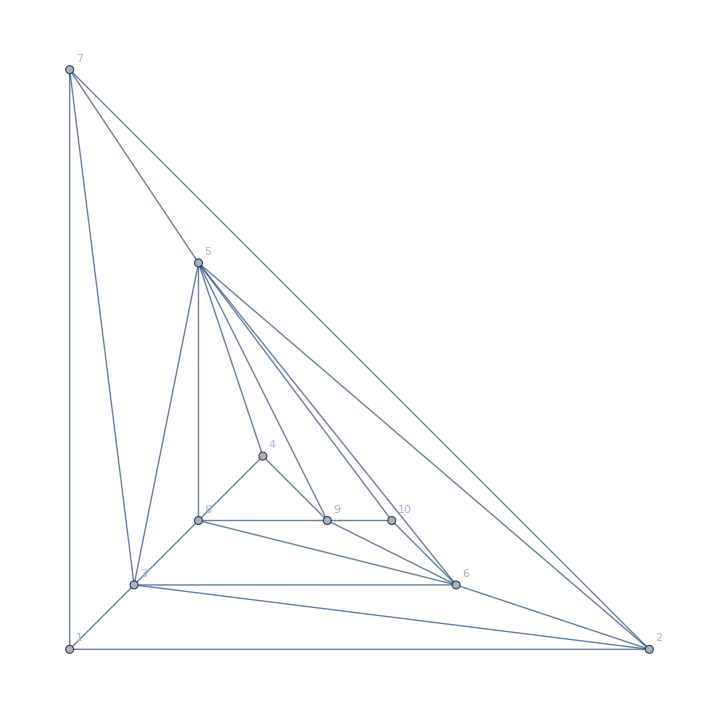

```mathematica
Graph[ReadGrof[144],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

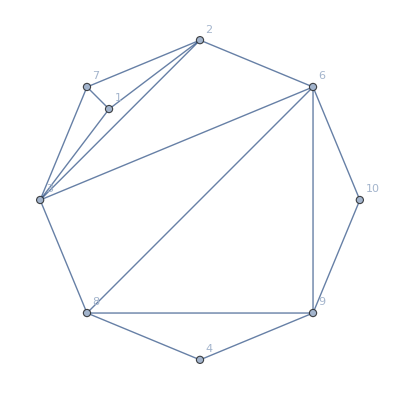

```mathematica
Graph[VertexDelete[ReadGrof[144],5],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

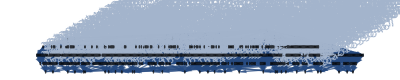

```mathematica
FindFullFormula[VertexDelete[ReadGrof[144],5]]//FormulaGraphReverse2
```

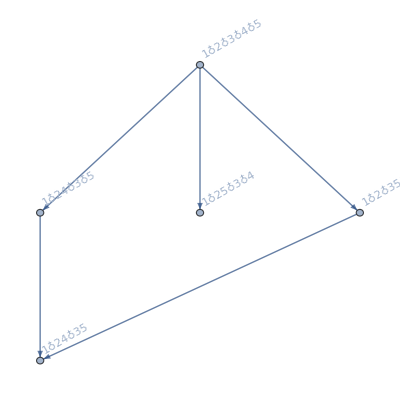

```mathematica
FindFullFormula[allGraphs5[amigo1,"graph"]]//FormulaGraphReverse2
```